Program calculating rate constants for van der Waals interaction for arbitrary boundary conditions at short range 
Everything in units of R_vdw and E_vdw (characteristic length and energy for van der Waals interaction)

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Oem\Desktop\Dipoles final

Parameters:
Lmax - maximal value of angular momentum L
xi - minimal value of r in the grid
nptl - number of points to tabulate the wavelenght
npt - numeber of point per de Broglie wavelenght in the grid 
energ - energy of particles
epsi - small number used to determine initial point of integration
epsf - small number used to determine final point of integration
dxf - step used to determine the final point of integration

Table of parametrs

```mathematica
Lmin=0;Lmax=20;nptl=500;npt=30;epsf=10^-12;epsi=10^-4;dxf=10;
```

```mathematica
KtoEh=3.1668153 10^(-6);
HztoEh=1.519829 10^(-16);
massunit=1.661 10^(-24)/(9.110 10^(-28));
μ=81.25 massunit; 
Debye=0.393456;
d=9/(137*2);
m = 9.18 BohrM;
```

```mathematica
C6=2277;
```

```mathematica
R6=(2 μ C6)^(1/4);E6=1/(2 μ R6^2);
```

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
C3=2d^2;R3=2 μ C3/R6;E3=(1/(2μ (R6 R3)^2))/E6;
β=R3
```

3.9669

```mathematica
xf=200;
```

```mathematica
freq=30000; 
freqz=0.1 freq;
ω=2 π freq HztoEh; ωz=2 π freqz HztoEh;aHO=(1/Sqrt[μ ω])/R6; aHOz=(1/Sqrt[μ ωz])/R6;
α=(1/aHO)^4;
αz=(1/aHOz)^4;
Ω=2 Sqrt[α];
Ωz=2 Sqrt[αz];
```

Potentials

```mathematica
Vho[l1_,ml1_,l2_,ml2_]:= (If[l1==l2,1,0]If[ml1==ml2,1,0]-(1-αz/α)If[ml1==ml2,1,0]/3((-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1] 2 ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}] + If[l1==l2,1,0]));
Vedd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];(*Dodać symbol wignera*)
Vmdd[l1_,ml1_,l2_,ml2_]:=-(-1)^ml1 Sqrt[2 l1 +1]Sqrt[2l2 +1]  ThreeJSymbol[{l1,0},{2,0},{l2,0}]ThreeJSymbol[{l1,-ml1},{2,0},{l2,ml2}];
Vvdw[l1_,ml1_,l2_,ml2_]:= -If[l1==l2,1,0]If[ml1==ml2,1,0];
```

```mathematica
Veddtab=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vmddtab=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vvdwtab=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vhotab=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,0,Lmax},{l2,0,Lmax}]]];
Vcftab = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,0,Lmax},{l2,0,Lmax}]]];
Veddtab2=Developer`ToPackedArray[N[Table[Vedd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vmddtab2=Developer`ToPackedArray[N[Table[Vmdd[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vvdwtab2=Developer`ToPackedArray[N[Table[Vvdw[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vhotab2=Developer`ToPackedArray[N[Table[Vho[l1,0,l2,0],{l1,1,Lmax},{l2,1,Lmax}]]];
Vcftab2 = Developer`ToPackedArray[N[Table[If[l1==l2,l1(l1+1),0],{l1,1,Lmax},{l2,1,Lmax}]]];
```

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{0,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{0,0},{2,0},{1,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{4,0}] is not triangular.

ClebschGordan::tri: ThreeJSymbol[{1,0},{2,0},{5,0}] is not triangular.

General::stop: Further output of ClebschGordan::tri will be suppressed during this calculation.

```mathematica
Vhotable[x_]:=N[(Table[Vhotab[[l1/2+1,l2/2+1]],{l1,0,Lmax},{l2,0,Lmax}])/.{r->x}];
```

Table of channels

```mathematica
TabCh={};Do[AppendTo[TabCh,{l(*,m*)}],{l,Lmin,Lmax}(*,{m,-l,l}*)];Nch=Length[TabCh];Id=IdentityMatrix[Lmax+1];Nch
```

21

Spherical Bessel functions

```mathematica
jl[l_,x_]:=Sqrt[Pi/(2x)]BesselJ[l+1/2,x];nl[l_,x_]:=(-1)^(l+1) Sqrt[Pi/(2x)]BesselJ[-l-1/2,x]
```

Matrix containg potential

```mathematica
V[r_]:=1/r^2 Vcftab + 1/r^6 Vvdwtab +β/r^3 Veddtab;
```

```mathematica
Length[V[1][[1]]]
```

21

Adiabatic potentials (diagonalized V[r]) + van der Waals potential

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.500061]].

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.565101]].

Take::take: Cannot take positions 1 through 10 in Eigenvalues[V2[0.638601]].

General::stop: Further output of Take::take will be suppressed during this calculation.

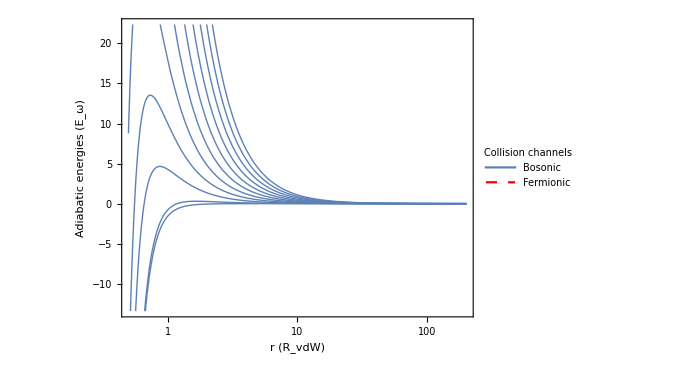

```mathematica
LogLinearPlot[{(Take[Sort[Eigenvalues[V[x]]],Lmax/2+1]),(Take[Sort[Eigenvalues[V2[x]]],Lmax/2])},{x,0.5,xf},
PlotRange->Automatic,AxesOrigin->{0.5,0},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},PlotLegends->Placed[LineLegend[{Style["Bosonic",FontFamily->"Times",FontWeight->Bold],Style["Fermionic",FontFamily->"Times",FontWeight->Bold]}, LegendLabel->Style["Collision channels",FontSize->14, FontFamily->"Times",FontWeight->Bold],LegendFunction->(Framed[#,RoundingRadius->0,Background->White]&),LegendMargins->5],{Left,Top}],FrameLabel->{Style["r (R_vdW)",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["Adiabatic energies (E_ω)",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
N[abar]*4
```

1.91196

Short range solution for van der Waals potential, with the short range phase "phi"

```mathematica
sol0[r_,A_,B_]=A Sqrt[r]BesselJ[1/4,1/(2 r^2)]+B Sqrt[r] BesselY[1/4,1/(2 r^2)];
```

```mathematica
ash[phi_]:=abar (1+Tan[phi])
```

```mathematica
as[y_,s_]:=abar(s+y(1+(1-s)^2)/(ⅈ+y(1-s)));
ap[y_,s_,k_]:=-2 abar1  (k abar)^2  (y+ⅈ(s-1))/(y s+ⅈ(s-2))
```

Table of short range solutions

```mathematica
Psi0[r_,A_,B_]:=Table[If[n1==n2,sol0[r,A,B],0] ,{n1,1,Nch},{n2,1,Nch}]
```

Subroutine performing outward integration using renormalized Numerov method
It takes Psi0 as an initial condition

Parameters:
en - energy
n0 -  starting point (element of xt)
nf -  final point (element of xt)
phi - short-range phase

```mathematica
evolNumOut[en_?NumericQ,n0_?IntegerQ,nf_?IntegerQ,A_?NumericQ,B_?NumericQ,cl_?IntegerQ]:=
Module[{W,Qt,n,Rinv,h,h0,Ro,Rprod},

nodes=0;

Rout[n0]=Psi0[xt[[n0+1]],A,B].Inverse[Psi0[xt[[n0]],A,B]];
h=xt[[n0+1]]-xt[[n0]];
n=n0+1;

While[n<=nf,
h0=h;
h=xt[[n+1]]-xt[[n]];
Which[

Abs[h]>1.5 Abs[h0],
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].(2 Id -(5h^2/6)QT[[n]]-(Id+(h^2/12)QT[[n-2]]).Inverse[Rout[n-1].Rout[n-2]]);,

Abs[h]<0.75 Abs[h0],
Qt=en Id-V[(xt[[n]]+xt[[n-1]])/2];
Rinv=Inverse[2 Id-(h0^2/12)Qt].((Id+(h0^2/12)QT[[n-1]]).Inverse[Rout[n-1]]+Id+(h0^2/12)QT[[n]]);
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)Qt).Rinv);,

True,
W=Id+(h^2/12) QT[[n+1]];
Rout[n]=Inverse[W].((2 Id -(5h^2/6)QT[[n]])-(Id+(h^2/12)QT[[n-1]]).Inverse[Rout[n-1]]);
];
n++;
];
Ro=Rout[nf];
Rprod=Inverse[Rout[n0]];Do[Rprod=Rprod.Inverse[Rout[n]],{n,n0+1,nf-1}];
Clear[W,n,Rinv,h,h0,Qt];
If[cl==1,Clear[Rout]];
{Ro,Rprod}]
```

Subroutine calculating K matrix

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix

```mathematica
KMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
K];
```

Subroutine calculating K and T matrices

Parameters:
en -  the energy
A,B - constants determining boundary conditions at short range 

Output:
K matrix
T matrix

```mathematica
KCTMatrix[en_?NumericQ,A_?NumericQ,B_?NumericQ]:=
Module[{J1,J2,N1,N2,Rn,K,r1,r2,kv,n1,n2,Rprod,R,W,T},
R=evolNumOut[en,1,nstep-1,A,B,1];
Rn=R[[1]];
Rprod=R[[2]];
kv=Sqrt[en];
r1=xt[[nstep-1]];
r2=xt[[nstep]];
J1=Table[If[n1==n2, kv r1 jl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
J2=Table[If[n1==n2,kv r2 jl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
N1=Table[If[n1==n2,kv r1 nl[TabCh[[n1,1]],kv r1],0],{n1,1,Nch},{n2,1,Nch}];
N2=Table[If[n1==n2,kv r2 nl[TabCh[[n1,1]],kv r2],0],{n1,1,Nch},{n2,1,Nch}];
K=-Inverse[Rn.N1-N2].(J2-Rn.J1);
W=Rprod.(J1+N1.K).Inverse[Id-ⅈ K];
R=ConjugateTranspose[W].W;
W=Inverse[Id-ⅈ K];
T=W.K/ Sqrt[en];
{T,K,Re[Tr[R]]}];
```

```mathematica
yy=0;ss=4.;
```

```mathematica
aS=as[yy,ss]
```

1.91196+0. ⅈ

```mathematica
aP=ap[yy,ss,Sqrt[en]]
```

-3.48683×10^-8+0. ⅈ

```mathematica
phi=φ/.Solve[aS==ash[φ],φ][[1]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

1.24905

```mathematica
abar=(Pi/8)/Gamma[5/4]^2;abar1=Gamma[1/4]^6/(144 Pi^2 Gamma[3/4]^2)abar ;
```

energies

```mathematica
en0=0.0001;enf=100.;de=(Log[enf]-Log[en0])/50;
```

```mathematica
TabEn=Table[Exp[ee],{ee,Log[en0],Log[enf],de}]
```

{0.0001,0.000131826,0.00017378,0.000229087,0.000301995,0.000398107,0.000524807,0.000691831,0.000912011,0.00120226,0.00158489,0.0020893,0.00275423,0.00363078,0.0047863,0.00630957,0.00831764,0.0109648,0.0144544,0.0190546,0.0251189,0.0331131,0.0436516,0.057544,0.0758578,0.1,0.131826,0.17378,0.229087,0.301995,0.398107,0.524807,0.691831,0.912011,1.20226,1.58489,2.0893,2.75423,3.63078,4.7863,6.30957,8.31764,10.9648,14.4544,19.0546,25.1189,33.1131,43.6516,57.544,75.8578,100.}

loop

```mathematica
Elastic={};Inelastic={}; Sections={};
Print["Progress:"];
Print[ProgressIndicator[Dynamic[counter],{1,Length[TabEn]}]];
Do[en=TabEn[[i]];
counter=i;
(*Print["en = ",en];*)

xi=0.1;
(*Determines the final point of integration*)
xf=400;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)

totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,{en,a0}];

Clear[xt,QT];
,{i,1,Length[TabEn]}
]
```

Progress:

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0465901,0.,1.08997×10^-6,0.,-5.16518×10^-8,0.,-3.05867×10^-11,0.,-2.52181×10^-14,0.,«11»},{0.,-0.0710489,0.,0.00004133,0.,2.24514×10^-8,0.,1.38843×10^-11,0.,1.16786×10^-14,«11»},{0.0000509158,0.,-0.0309527,0.,0.0000172131,0.,5.42713×10^-9,0.,3.48072×10^-12,0.,«11»},{0.,-0.0000421706,0.,-0.037791,0.,0.0000164317,0.,4.83554×10^-9,0.,3.08741×10^-12,«11»},{2.19142×10^-8,0.,-1.56331×10^-7,0.,-0.0700282,0.,0.0000252574,0.,7.43314×10^-9,0.,«11»},{0.,-7.57909×10^-9,0.,5.43614×10^-6,«3»,0.0000554707,0.,1.60012×10^-8,«11»},{3.50107×10^-12,0.,-1.32977×10^-11,0.,6.81376×10^-6,0.,-0.508825,0.,0.000156756,0.,«11»},{0.,-7.65201×10^-13,0.,2.6117×10^-10,0.,9.05547×10^-6,0.,-1.79481,0.,0.000535259,«11»},{3.00505×10^-16,0.,-8.87849×10^-16,0.,2.08749×10^-10,0.,0.0000163175,0.,-7.28487,0.,«11»},{0.,-4.7285×10^-17,0.,1.22503×10^-14,0.,1.91894×10^-10,0.,0.0000393189,0.,-33.397,«11»},«11»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0397648,0.,0.0000433369,0.,-4.56359×10^-8,0.,-2.11482×10^-11,0.,-1.17669×10^-14,0.,«11»},{0.,0.47209,0.,-0.000132735,0.,-1.28201×10^-7,0.,-5.55878×10^-11,0.,-3.3657×10^-14,«11»},{0.0000112216,0.,-0.0419305,0.,0.0000190114,0.,5.46762×10^-9,0.,2.50788×10^-12,0.,«11»},{0.,0.000308297,0.,-0.035602,0.,0.000013867,0.,3.06918×10^-9,0.,1.44938×10^-12,«11»},{5.21803×10^-9,0.,-8.39473×10^-6,0.,-0.0523048,0.,0.000016226,0.,3.54001×10^-9,0.,«11»},{0.,6.78113×10^-8,0.,3.15785×10^-6,«3»,0.0000279583,0.,6.09114×10^-9,«11»},{8.474×10^-13,0.,-8.4606×10^-10,0.,5.68593×10^-6,0.,-0.263187,0.,0.0000644644,0.,«11»},{0.,7.24131×10^-12,0.,1.72127×10^-10,0.,6.88503×10^-6,0.,-0.787157,0.,0.00018378,«11»},{7.27935×10^-17,0.,-5.99128×10^-14,0.,1.91511×10^-10,0.,9.95168×10^-6,0.,-2.72544,0.,«11»},{0.,4.58814×10^-16,0.,8.50599×10^-15,0.,1.56964×10^-10,0.,0.0000192301,0.,-10.7013,«11»},«11»} may contain significant numerical errors.

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0516593,0.,0.000209719,0.,-7.9164×10^-8,0.,-3.77606×10^-11,0.,-1.38192×10^-14,0.,«11»},{0.,0.0679749,0.,5.62904×10^-6,0.,-1.82246×10^-8,0.,-6.03509×10^-12,0.,-2.59291×10^-15,«11»},{-0.000110429,0.,-0.0923044,0.,0.0000277923,0.,1.03492×10^-8,0.,3.4092×10^-12,0.,«11»},{0.,0.000035519,0.,-0.0399969,0.,0.0000138459,0.,2.61027×10^-9,0.,9.10457×10^-13,«11»},{-5.05357×10^-8,0.,-0.0000336931,0.,-0.0442231,0.,0.0000125817,0.,2.08248×10^-9,0.,«11»},{0.,9.70222×10^-9,0.,-1.16814×10^-6,«4»,0.,2.76614×10^-9,«11»},{-8.16159×10^-12,0.,-4.24804×10^-9,0.,4.2597×10^-6,0.,-0.150308,0.,0.0000306291,0.,«11»},{0.,1.1055×10^-12,0.,-7.57727×10^-11,0.,5.73505×10^-6,0.,-0.380332,0.,0.0000720243,«11»},{-6.93833×10^-16,0.,-3.25062×10^-13,0.,1.63775×10^-10,0.,7.11434×10^-6,0.,-1.12373,0.,«11»},{0.,7.23335×10^-17,0.,-4.02492×10^-15,0.,1.44932×10^-10,0.,0.0000109677,0.,-3.78614,«11»},«11»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

{{0.0001,0.0000935116},{0.000131826,0.000113685},{0.00017378,0.000141221},{0.000229087,0.000182371},{0.000301995,0.00023644},{0.000398107,0.00030009},{0.000524807,0.000386993},{0.000691831,0.000502854},{0.000912011,0.000650583},{0.00120226,0.000849019},{0.00158489,0.0011083},{0.0020893,0.00144897},{0.00275423,0.00190003},{0.00363078,0.00249492},{0.0047863,0.00327847},{0.00630957,0.00431439},{0.00831764,0.00568165},{0.0109648,0.00748799},{0.0144544,0.00987125},{0.0190546,0.0130136},{0.0251189,0.0171508},{0.0331131,0.0225842},{0.0436516,0.0296984},{0.057544,0.0389738},{0.0758578,0.0509964},{0.1,0.0664591},{0.131826,0.0861397},{0.17378,0.110839},{0.229087,0.141256},{0.301995,0.177757},{0.398107,0.219998},{0.524807,0.266382},{0.691831,0.313352},{0.912011,0.354725},{1.20226,0.381599},{1.58489,0.384137},{2.0893,0.358115},{2.75423,0.32172},{3.63078,0.349902},{4.7863,0.619444},{6.30957,1.38522},{8.31764,2.72826},{10.9648,4.2916},{14.4544,5.88633},{19.0546,7.28154},{25.1189,8.3115},{33.1131,10.0571},{43.6516,11.7513},{57.544,13.2605},{75.8578,14.4588},{100.,19.8033}}

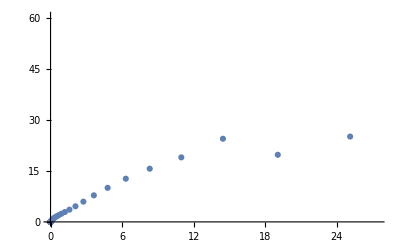

```mathematica
Inelastic
ListPlot[Elastic]
```

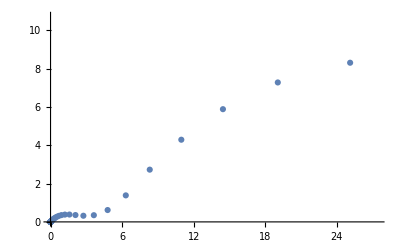

```mathematica
ListPlot[Inelastic]
```

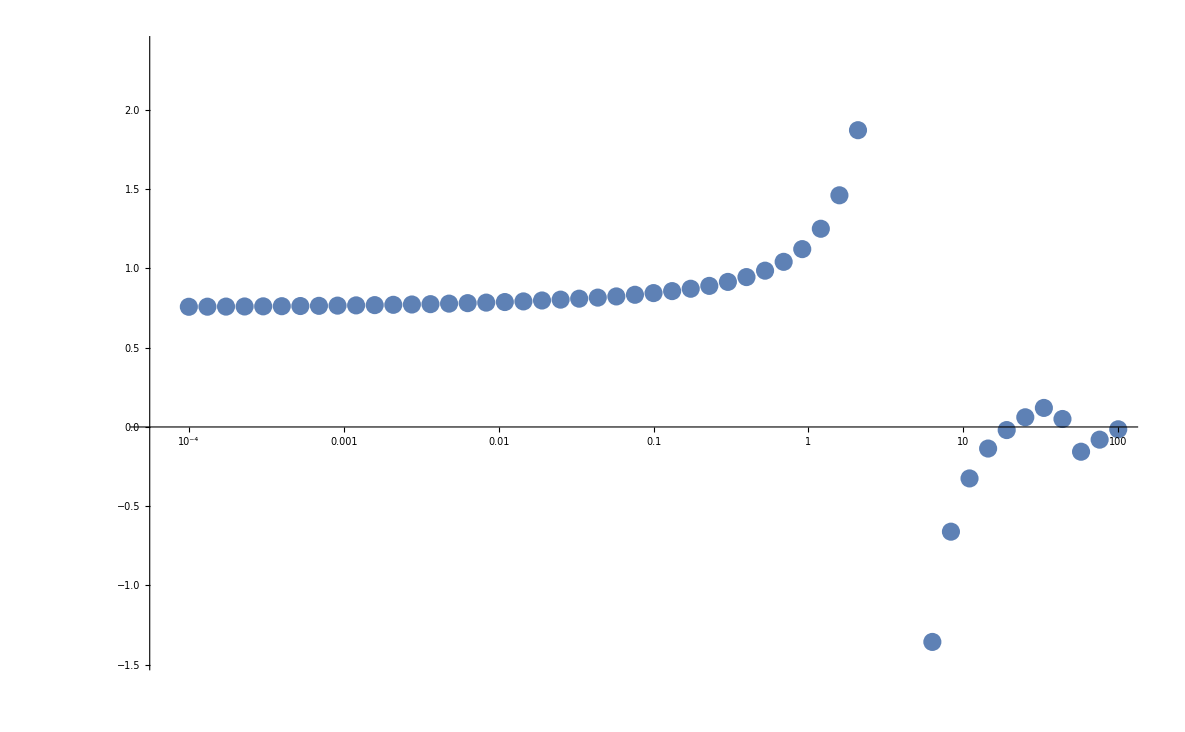

```mathematica
ListLogLinearPlot[Re[Sections]]
```

```mathematica
Re[Sections]
```

{{0.0001,0.758192},{0.000131826,0.758751},{0.00017378,0.759369},{0.000229087,0.760079},{0.000301995,0.760913},{0.000398107,0.761852},{0.000524807,0.762902},{0.000691831,0.764113},{0.000912011,0.765458},{0.00120226,0.766979},{0.00158489,0.768679},{0.0020893,0.770545},{0.00275423,0.772557},{0.00363078,0.774763},{0.0047863,0.778078},{0.00630957,0.781122},{0.00831764,0.784466},{0.0109648,0.788111},{0.0144544,0.792033},{0.0190546,0.797864},{0.0251189,0.803279},{0.0331131,0.809316},{0.0436516,0.816019},{0.057544,0.823479},{0.0758578,0.833881},{0.1,0.844521},{0.131826,0.857023},{0.17378,0.871926},{0.229087,0.889992},{0.301995,0.91508},{0.398107,0.9455},{0.524807,0.985967},{0.691831,1.04172},{0.912011,1.1219},{1.20226,1.25037},{1.58489,1.46145},{2.0893,1.8721},{2.75423,2.95162},{3.63078,11.8239},{4.7863,-3.83963},{6.30957,-1.35603},{8.31764,-0.660532},{10.9648,-0.324679},{14.4544,-0.136108},{19.0546,-0.0195552},{25.1189,0.0610449},{33.1131,0.120131},{43.6516,0.0503153},{57.544,-0.156178},{75.8578,-0.0800751},{100.,-0.0146771}}

Imports

```mathematica
imported = Import["Drop_3D_30_07.csv"];
imported=Sort[imported,#1[[2]]<#2[[2]]&];
scat=Transpose[imported][[1]];
scat = (1/aHOz)*scat;
scat=1/scat;

energies=Transpose[imported][[2]];
energies = Ωz * energies;

colored = Join[Transpose[imported], {Range[Length[scat]]}];
```

```mathematica
Export["Before_scat_colored.csv",Transpose[colored]]
```

Before_scat_colored.csv

Calculations

```mathematica
Elastic={};Inelastic={}; Sections={};Scattered={}; Sections1D={};
en = 0.0000001;
Print["Progress:"];
Print[ProgressIndicator[Dynamic[k],{1,Length[scat]}]];
Do[aS=scat[[i]];
k=i;
(*Print["as = ",aS];*)

xi=0.1;
(*Determines the final point of integration*)
xf=200;

(* Subroutine determining steps *)
Module[{eig,h,dbl,n,pxi,pxf,dp,x,p,tab},

pxi=Log[xi ];
pxf=Log[xf +dxf];
dp=(pxf-pxi)/nptl;
tab=Table[x=Exp[p];eig=Eigenvalues[V[x]];{x,Min[2Pi/Sqrt[Abs[en-eig]]]},{p,pxi,pxf,dp}];
lambda=Interpolation[tab]; (*Local de Broglie wavelength (minimum over all channels). Used for determination of the step size *)

xt={};
h=lambda[xi]/npt;
AppendTo[xt,xi];
AppendTo[xt,xi+h];
dbl=1; (* dbl = 1 - step doubling or halving was done in the previous step, dbl = 0 otherwise *)
n=2;

While[(xt[[n]]<xf)||(dbl==1),
Which[
(lambda[xt[[n]]]≥2 npt h)&&(dbl==0),

h=2h;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

(lambda[xt[[n]]]<npt h)&&(dbl==0),

h=h/2;
AppendTo[xt,xt[[n]]+h];
dbl=1;,

True,


AppendTo[xt,xt[[n]]+h];
dbl=0;
];
n++;
];
nstep=n;  (* Total number of steps *);
];
(*Print["nstep = ",nstep];*)
QT=Table[en Id-V[xt[[n]]],{n,1,Length[xt]}];
phi=φ/.Solve[aS==ash[φ],φ][[1]];
Kmatr=KMatrix[en,Sin[phi],Cos[phi]];
Smatr=(Id+ⅈ Kmatr).Inverse[Id-ⅈ Kmatr];
S0 = N[Smatr[[1,1]]];
a0 = 1/(ⅈ Sqrt[en])(1-S0)/(1+S0);

(*totinelS=Pi Sum[1-Abs[Smatr[[n1,n1]]]^2,{n1,1,1}]/en;
totelS=Pi Sum[Abs[1-Smatr[[n1,n1]]]^2,{n1,1,1}]/en;*)
(*Print[a0];*)
totInEl= Sum[(2TabCh[[n1,1]]+1)(1-Abs[Smatr[[n1,n1]]]^2),{n1,1,Nch}];
totEl=  Sum[(2TabCh[[n1,1]]+1)Abs[1-Smatr[[n1,n1]]]^2,{n1,1,Nch}];

AppendTo[Elastic,{en,totEl}];
AppendTo[Inelastic,{en,totInEl}];
AppendTo[Sections,Re[a0]];
AppendTo[Sections1D,imported[[i,3]]];
AppendTo[Scattered,{aS,Re[a0]}];

Clear[xt,QT];
,{i,1,Length[scat]}
]
```

Progress:

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.0087238,0.,0.0292066,0.,0.107935,0.,0.724824,0.,5.73794,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.0952,0.,18.2444,0.,131.116,«11»},{0.0000383657,0.,-32.7298,0.,75.9167,0.,199.909,0.,1084.34,0.,«11»},{0.,0.000274466,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{1.60129×10^-8,0.,0.00857356,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.12267×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{4.29252×10^-12,0.,9.01188×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34435×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{6.88646×10^-16,0.,9.90599×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.29324×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

Part::partw: Part 3 of {17.3402,-19.9526} does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00882281,0.,0.0288612,0.,0.105305,0.,0.701565,0.,5.52011,0.,«11»},{0.,-0.411054,0.,1.04032,0.,3.09523,0.,18.2447,0.,131.119,«11»},{0.000037912,0.,-32.7298,0.,75.9167,0.,199.909,0.,1084.34,0.,«11»},{0.,0.000274467,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{1.56227×10^-8,0.,0.00857356,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.12272×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{4.15476×10^-12,0.,9.01188×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34448×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{6.62501×10^-16,0.,9.90598×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.29345×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

Part::partw: Part 3 of {-16.4754,-19.9526} does not exist.

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of Solve::ifun will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{-0.00876196,0.,0.0290697,0.,0.106878,0.,0.715392,0.,5.649,0.,«11»},{0.,-0.411053,0.,1.04033,0.,3.09525,0.,18.2448,0.,131.12,«11»},{0.0000381858,0.,-32.7298,0.,75.9167,0.,199.909,0.,1084.34,0.,«11»},{0.,0.000274468,0.,-3645.5,0.,8145.87,0.,19850.3,0.,101834.,«11»},{1.58561×10^-8,0.,0.00857356,0.,-522024.,0.,1.14504×10^6,0.,2.64028×10^6,0.,«11»},{0.,5.12275×10^-8,0.,0.510977,0.,-9.13644×10^7,0.,1.98539×10^8,0.,4.38778×10^8,«11»},{4.23665×10^-12,0.,9.01188×10^-7,0.,45.7045,0.,-1.88983×10^10,0.,4.08954×10^10,0.,«11»},{0.,8.34455×10^-12,0.,0.0000344092,0.,5486.15,0.,-4.51052×10^12,0.,9.75092×10^12,«11»},{6.7797×10^-16,0.,9.90599×10^-11,0.,0.00213562,0.,828684.,0.,-1.22011×10^15,0.,«11»},{0.,9.29356×10^-16,0.,2.7355×10^-9,0.,0.187885,0.,1.51095×10^8,0.,-3.68882×10^17,«11»},«11»} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Part::partw: Part 3 of {-11.9927,-19.9526} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Spectral=Join[{aHOz/Sections},{energies/Ωz}];
Spectral1=Join[{aHOz/Sections},{energies/Ωz},{Sections1D}];
Spectral1=Transpose[Spectral1];
Spectral=Transpose[Spectral];
Spectral
```

{{4.28583,-19.9526},{2.14948,-19.9526},{3.09296,-19.9526},{3.57267,-15.8489},{2.07831,-15.8489},{2.66067,-15.8489},{73.1626,-12.5893},{2.96231,-12.5893},{1.91486,-12.5893},{2.37588,-12.5893},{2.43992,-10.},{1.6296,-10.},{2.25981,-10.},{1.99363,-7.94328},{1.31725,-7.94328},{2.21425,-7.94328},{1.61367,-6.30957},{1.02435,-6.30957},{2.19039,-6.30957},{1.2917,-5.01187},{0.761705,-5.01187},{2.1754,-5.01187},{1.02042,-3.98107},{0.531261,-3.98107},{2.16505,-3.98107},{0.793285,-3.16228},{0.332181,-3.16228},{0.604326,-2.51189},{0.162392,-2.51189},{2.15188,-2.51189},{0.448117,-1.99526},{0.0192021,-1.99526},{2.14758,-1.99526},{0.319745,-1.58489},{-0.100374,-1.58489},{0.214818,-1.25893},{-0.199382,-1.25893},{0.129465,-1.},{-0.280761,-1.},{0.0603213,-0.794328},{-0.347235,-0.794328},{0.00450804,-0.630957},{-0.401253,-0.630957},{-0.0404106,-0.501187},{-0.444959,-0.501187},{-0.0764716,-0.398107},{-0.480196,-0.398107},{-0.105362,-0.316228},{-0.508524,-0.316228},{-0.12847,-0.251189},{-0.531242,-0.251189},{-0.146927,-0.199526},{-0.549427,-0.199526},{-0.161653,-0.158489},{-0.563961,-0.158489},{-0.173392,-0.125893},{-0.575563,-0.125893},{-0.182743,-0.1},{-0.584815,-0.1},{-0.190187,-0.0794328},{-0.592187,-0.0794328},{-0.196111,-0.0630957},{-0.598057,-0.0630957},{-0.200823,-0.0501187},{-0.602729,-0.0501187},{-0.204571,-0.0398107},{-0.606446,-0.0398107},{-0.20755,-0.0316228},{-0.609402,-0.0316228},{-0.209918,-0.0251189},{-0.611753,-0.0251189},{-0.211801,-0.0199526},{-0.613622,-0.0199526},{-0.213297,-0.0158489},{-0.615107,-0.0158489},{-0.214485,-0.0125893},{-0.616287,-0.0125893},{-0.21543,-0.01},{-0.617225,-0.01},{-0.21618,-0.00794328},{-0.617971,-0.00794328},{-0.216776,-0.00630957},{-0.618563,-0.00630957},{-0.21725,-0.00501187},{-0.619033,-0.00501187},{-0.217626,-0.00398107},{-0.619407,-0.00398107},{-0.217925,-0.00316228},{-0.619704,-0.00316228},{-0.218162,-0.00251189},{-0.61994,-0.00251189},{-0.218351,-0.00199526},{-0.620127,-0.00199526},{-0.218501,-0.00158489},{-0.620276,-0.00158489},{-0.21862,-0.00125893},{-0.620394,-0.00125893},{-0.218714,-0.001},{-0.620488,-0.001},{-0.219445,0.001},{-0.621214,0.001},{-0.248776,0.081},{-0.650402,0.081},{-0.278343,0.161},{-0.679914,0.161},{-0.308151,0.241},{-0.709755,0.241},{-0.338205,0.321},{-0.739935,0.321},{-0.36851,0.401},{-0.770459,0.401},{-0.399072,0.481},{-0.801336,0.481},{-0.429896,0.561},{-0.832573,0.561},{-0.460987,0.641},{-0.86418,0.641},{-0.492354,0.721},{-0.896164,0.721},{-0.524,0.801},{-0.928534,0.801},{-0.555933,0.881},{-0.961299,0.881},{-0.588159,0.961},{-0.994469,0.961},{-0.620686,1.041},{-1.02805,1.041},{-0.65352,1.121},{-1.06206,1.121},{-0.686669,1.201},{-1.09651,1.201},{-0.72014,1.281},{-1.1314,1.281},{-0.753941,1.361},{-1.16674,1.361},{-0.78808,1.441},{-1.20256,1.441},{-0.822566,1.521},{-1.23885,1.521},{-0.857407,1.601},{-1.27564,1.601},{-0.892612,1.681},{-1.31294,1.681},{-0.928192,1.761},{-1.35075,1.761},{-0.964154,1.841},{-1.3891,1.841},{-1.00051,1.921},{-1.428,1.921},{-1.03727,2.001},{-1.46746,2.001},{-1.07445,2.081},{-1.50749,2.081},{-1.11205,2.161},{-1.54813,2.161},{-1.15009,2.241},{-1.58937,2.241},{-1.18858,2.321},{-1.63124,2.321},{-1.22753,2.401},{-1.67377,2.401},{-1.26696,2.481},{-1.71695,2.481},{-1.30688,2.561},{-1.76083,2.561},{-1.3473,2.641},{-1.80541,2.641},{-1.38824,2.721},{-1.85073,2.721},{-1.42972,2.801},{-1.89679,2.801},{-1.47175,2.881},{-1.94363,2.881},{-1.51434,2.961},{-1.99128,2.961},{-1.55753,3.041},{-2.03975,3.041},{-1.60131,3.121},{-2.08907,3.121},{-1.64572,3.201},{-2.13927,3.201},{-1.69078,3.281},{-2.19039,3.281},{-1.7365,3.361},{-2.24245,3.361},{-1.7829,3.441},{-2.29548,3.441},{-1.83002,3.521},{-2.34953,3.521},{-1.87787,3.601},{-2.40462,3.601},{-1.92648,3.681},{-2.46079,3.681},{-1.97588,3.761},{-2.51809,3.761},{-2.0261,3.841},{-2.57655,3.841},{2.10525,3.841},{-2.07716,3.921},{-2.63622,3.921},{2.10471,3.921},{-2.1291,4.001},{-2.69715,4.001},{2.10418,4.001},{-2.18195,4.081},{-2.75938,4.081},{2.10364,4.081},{-2.23574,4.161},{-2.82297,4.161},{2.10311,4.161},{-2.29051,4.241},{-2.88797,4.241},{2.10257,4.241},{-2.34631,4.321},{-2.95443,4.321},{2.10204,4.321},{-2.40316,4.401},{-3.02243,4.401},{2.10151,4.401},{-2.46112,4.481},{-3.09202,4.481},{2.10097,4.481},{-2.52022,4.561},{-3.16328,4.561},{2.10044,4.561},{-2.58052,4.641},{-3.23627,4.641},{2.09991,4.641},{-2.64208,4.721},{-3.31107,4.721},{2.09937,4.721},{-2.70493,4.801},{-3.38777,4.801},{2.09884,4.801},{-2.76914,4.881},{-3.46645,4.881},{2.09831,4.881},{-2.83478,4.961},{-3.54721,4.961},{2.09778,4.961},{-2.9019,5.041},{-3.63014,5.041},{2.09725,5.041},{-2.97058,5.121},{-3.71535,5.121},{2.09671,5.121},{-3.04089,5.201},{-3.80296,5.201},{2.09618,5.201},{-3.11291,5.281},{-3.89309,5.281},{2.09565,5.281},{-3.18672,5.361},{-3.98586,5.361},{2.09512,5.361},{-3.26242,5.441},{-4.08142,5.441},{2.09459,5.441},{-3.3401,5.521},{-4.17992,5.521},{2.09406,5.521},{-3.41987,5.601},{-4.28151,5.601},{2.09353,5.601},{-3.50183,5.681},{-4.38638,5.681},{2.09299,5.681},{-3.58611,5.761},{-4.4947,5.761},{2.09246,5.761},{-3.67284,5.841},{-4.6067,5.841},{2.09193,5.841},{-3.76216,5.921},{-4.72257,5.921},{2.0914,5.921},{-3.85422,6.001},{-4.84257,6.001},{2.09087,6.001},{-3.94918,6.081},{-4.96695,6.081},{2.09034,6.081},{-4.04722,6.161},{-5.096,6.161},{2.0898,6.161},{-4.14853,6.241},{-5.23003,6.241},{2.08927,6.241},{-4.25334,6.321},{-5.36936,6.321},{2.08874,6.321},{-4.36185,6.401},{-5.51438,6.401},{2.0882,6.401},{-4.47433,6.481},{-5.66549,6.481},{2.08767,6.481},{-4.59106,6.561},{-5.82314,6.561},{2.08713,6.561},{-4.71232,6.641},{-5.98782,6.641},{2.0866,6.641},{-4.83847,6.721},{-6.16007,6.721},{2.08606,6.721},{-4.96985,6.801},{-6.34051,6.801},{2.08553,6.801},{-5.10689,6.881},{-6.52982,6.881},{-5.25002,6.961},{-6.72874,6.961},{-5.39976,7.041},{-6.93812,7.041},{-5.55665,7.121},{-7.15891,7.121},{-5.72134,7.201},{-7.39219,7.201},{-5.89452,7.281},{-7.63916,7.281},{-6.07699,7.361},{-7.90122,7.361},{-6.26965,7.441},{-8.17995,7.441},{-6.47353,7.521},{-8.47716,7.521},{-6.6898,7.601},{-8.79494,7.601},{-6.9198,7.681},{-9.13573,7.681},{-7.16509,7.761},{-9.50238,7.761},{-7.42748,7.841},{-9.89823,7.841},{-7.70907,7.921},{-10.3272,7.921},{-8.01236,8.001},{-10.7941,8.001},{-8.3403,8.081},{-11.3045,8.081},{-8.69643,8.161},{-11.8655,8.161},{-9.08504,8.241},{-12.4853,8.241},{-9.51142,8.321},{-13.1746,8.321},{-9.98216,8.401},{-13.9466,8.401},{-10.5058,8.481},{-14.8181,8.481},{-11.0935,8.561},{-15.811,8.561},{-11.7617,8.641},{-16.9542,8.641},{-12.537,8.721},{-18.2866,8.721},{-13.4813,8.801},{-19.862,8.801},{-14.9479,8.881},{-21.7571,8.881},{-14.0431,8.961},{-24.0849,8.961},{-16.2334,9.041},{-27.0193,9.041},{-17.9865,9.121},{-30.8429,9.121},{-20.0347,9.201},{-36.0471,9.201},{-22.5927,9.281},{-43.5703,9.281},{-25.9313,9.361},{-55.4547,9.361},{-30.5055,9.441},{-77.1483,9.441},{-37.1847,9.521},{-129.688,9.521},{-47.8856,9.601},{-445.553,9.601},{-67.8472,9.681},{287.376,9.681},{-118.351,9.761},{105.114,9.761},{-499.121,9.841},{62.8156,9.841},{216.879,9.921},{43.9117,9.921},{2.06259,9.921},{87.7035,10.001},{33.1547,10.001},{2.06184,10.001},{54.2031,10.081},{26.1862,10.081},{2.06106,10.081},{38.8852,10.161},{21.2892,10.161},{2.06025,10.161},{30.0261,10.241},{17.65,10.241},{2.05939,10.241},{24.2192,10.321},{14.8321,10.321},{2.0585,10.321},{20.0885,10.401},{12.5795,10.401},{2.05754,10.401},{16.9732,10.481},{10.7312,10.481},{2.0565,10.481},{14.517,10.561},{9.18046,10.561},{2.05538,10.561},{12.5104,10.641},{7.85344,10.641},{10.8221,10.721},{6.69709,10.721},{9.36462,10.801},{5.67214,10.801},{8.07699,10.881},{4.74858,10.881},{3.90278,10.961},{6.91364,10.961},{3.11545,11.041},{5.83602,11.041},{2.37016,11.121},{4.78801,11.121},{1.65224,11.201},{4.61475,11.201},{0.947746,11.281},{3.12206,11.281},{0.24249,11.361},{1.83514,11.361},{2.32057,11.361},{-0.479061,11.441},{1.07731,11.441},{2.11502,11.441},{-1.23526,11.521},{0.104052,11.521},{2.08493,11.521},{-2.04942,11.601},{-0.965506,11.601},{2.074,11.601},{-2.95326,11.681},{-2.16477,11.681},{2.06816,11.681},{-3.99292,11.761},{-3.55999,11.761},{2.06436,11.761},{-5.24022,11.841},{-5.26116,11.841},{-6.81599,11.921},{-7.46302,11.921},{-8.94486,12.001},{-10.5503,12.001},{-12.1346,12.081},{-15.4142,12.081},{-16.8405,12.161},{-24.7214,12.161},{-27.6429,12.241},{-51.8818,12.241},{-63.5225,12.321},{5195.45,12.321},{338.427,12.401},{52.1223,12.401},{49.3585,12.481},{25.837,12.481},{27.3451,12.561},{16.8175,12.561},{19.0618,12.641},{12.1886,12.641},{14.5994,12.721},{9.33053,12.721},{11.7323,12.801},{7.35665,12.801},{9.6806,12.881},{5.88316,12.881},{8.09859,12.961},{4.71676,12.961},{3.74917,13.041},{6.80676,13.041},{2.91441,13.121},{5.6971,13.121},{2.16918,13.201},{2.02553,13.201},{4.66904,13.201},{1.48298,13.281},{2.01542,13.281},{4.43908,13.281},{0.832569,13.361},{1.99219,13.361},{3.18927,13.361},{0.198549,13.441},{1.89307,13.441},{2.44138,13.441},{-0.437005,13.521},{1.37699,13.521},{0.585796,13.601},{-0.28906,13.681},{-3.42932,13.841},{-2.37576,13.841},{-4.46845,13.921},{-3.71532,13.921},{-5.76969,14.001},{-5.41622,14.001},{-7.50849,14.081},{-7.73916,14.081},{-10.0504,14.161},{-11.2546,14.161},{-14.8433,14.241},{-17.5164,14.241},{-22.2646,14.321},{-32.8761,14.321},{-48.6663,14.401},{-152.357,14.401},{554.596,14.481},{61.3574,14.481},{44.6469,14.561},{25.1699,14.561},{24.0192,14.641},{15.429,14.641},{16.6027,14.721},{10.8281,14.721},{12.6735,14.801},{8.10515,14.801},{10.1688,14.881},{6.26985,14.881},{8.38282,14.961},{4.91939,14.961},{3.85908,15.041},{7.00593,15.041},{2.98291,15.121},{5.87614,15.121},{2.22757,15.201},{4.88165,15.201},{1.55209,15.281},{2.88793,15.281},{0.927767,15.361},{3.49809,15.361},{0.332738,15.441},{1.94689,15.441},{2.74653,15.441},{-0.251405,15.521},{1.72106,15.521},{2.23371,15.521},{-0.841988,15.601},{1.11769,15.601},{2.10234,15.601},{-1.45738,15.681},{0.388099,15.681},{2.07183,15.681},{-2.11943,15.761},{-0.414177,15.761},{-2.85695,15.841},{-1.3144,15.841},{-3.71148,15.921},{-2.36317,15.921},{-4.74828,16.001},{-3.64457,16.001},{-6.07933,16.081},{-5.30739,16.081},{-7.91855,16.161},{-7.64553,16.161},{-10.7466,16.241},{-11.3403,16.241},{-14.841,16.321},{-18.4383,16.321},{-27.0615,16.401},{-39.3804,16.401},{-89.1131,16.481},{1218.39,16.481},{2.0303,16.481},{79.1154,16.561},{37.6029,16.561},{2.02847,16.561},{28.7309,16.641},{18.6043,16.641},{2.02661,16.641},{17.9319,16.721},{11.9791,16.721},{2.02466,16.721},{13.0929,16.801},{8.55347,16.801},{2.02256,16.801},{10.2655,16.881},{6.42022,16.881},{2.02023,16.881},{8.35676,16.961},{4.93126,16.961},{2.01755,16.961},{3.80598,17.041},{6.9405,17.041},{2.90297,17.121},{5.81111,17.121},{2.14261,17.201},{4.83709,17.201},{1.47598,17.281},{2.81194,17.281},{0.87045,17.361},{3.54782,17.361},{0.302421,17.441},{1.94421,17.441},{2.8401,17.441},{-0.246837,17.521},{1.79706,17.521},{2.31188,17.521},{-0.79386,17.601},{1.33081,17.601},{2.11822,17.601},{-1.35507,17.681},{0.705109,17.681},{2.07319,17.681},{-1.94886,17.761},{0.0166382,17.761},{-2.59821,17.841},{-0.743507,17.841},{-3.33475,17.921},{-1.60925,17.921},{-4.20601,18.001},{-2.63698,18.001},{-5.28972,18.081},{-3.9217,18.081},{-6.72569,18.161},{-5.63802,18.161},{-8.79854,18.241},{-8.14991,18.241},{-12.2357,18.321},{-12.3732,18.321},{-18.4763,18.401},{-21.5004,18.401},{-38.6819,18.481},{-60.2848,18.481},{1376.94,18.561},{87.084,18.561},{38.8965,18.641},{24.8909,18.641},{20.3248,18.721},{14.0041,18.721},{13.8939,18.801},{9.38224,18.801},{10.5388,18.881},{6.77847,18.881},{8.4184,18.961},{5.07133,18.961},{3.83648,19.041},{6.91354,19.041},{2.87787,19.121},{5.7519,19.121},{2.09201,19.201},{4.77175,19.201},{1.4185,19.281},{0.364129,19.281},{0.819027,19.361},{1.96801,19.361},{3.53504,19.361},{0.267249,19.441},{1.933,19.441},{2.86906,19.441},{-0.256514,19.521},{1.81495,19.521},{2.36203,19.521},{-0.768457,19.601},{1.44312,19.601},{2.13505,19.601},{-1.28344,19.681},{0.906237,19.681},{2.0759,19.681},{-1.81682,19.761},{0.3153,19.761},{2.05379,19.761},{-2.38638,19.841},{-0.324539,19.841},{2.04226,19.841},{-3.01501,19.921},{-1.03359,19.921},{2.03499,19.921}}

```mathematica
Export["Spectral_02.csv",Spectral];
Export["Spectral_colored.csv",Spectral1];
```

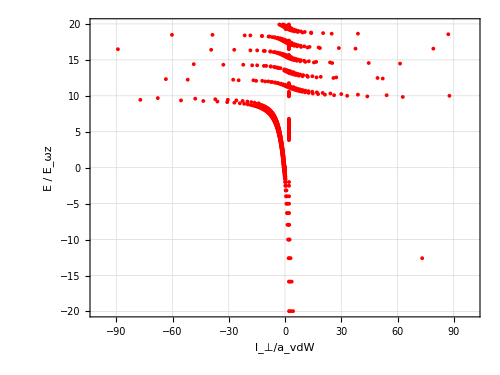

```mathematica
ListPlot[Re[Spectral],PlotRange->{{-100,100},All},
AspectRatio->0.75,
Frame->True, FrameStyle->{{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]},{Directive[Thickness[0.005],Black],Directive[Thickness[0.005],Black]}},
PlotStyle->{Thick,{Red,Dashed}},FrameLabel->{Style["l_⊥/a_vdW",FontSize->20, FontFamily->"Times New Roman",FontWeight->Bold],Style["E / E_ωz",FontSize->20,FontWeight->Bold, FontFamily->"Times"]},GridLines->Automatic, GridLinesStyle->Directive[Thin, Dashed, LightGray],ImagePadding->50,ImageSize->500]
```

```mathematica
Spectral
```

{{4.28583,-19.9526},{2.14948,-19.9526},{3.09296,-19.9526},{3.57267,-15.8489},{2.07831,-15.8489},{2.66067,-15.8489},{73.1626,-12.5893},{2.96231,-12.5893},{1.91486,-12.5893},{2.37588,-12.5893},{2.43992,-10.},{1.6296,-10.},{2.25981,-10.},{1.99363,-7.94328},{1.31725,-7.94328},{2.21425,-7.94328},{1.61367,-6.30957},{1.02435,-6.30957},{2.19039,-6.30957},{1.2917,-5.01187},{0.761705,-5.01187},{2.1754,-5.01187},{1.02042,-3.98107},{0.531261,-3.98107},{2.16505,-3.98107},{0.793285,-3.16228},{0.332181,-3.16228},{0.604326,-2.51189},{0.162392,-2.51189},{2.15188,-2.51189},{0.448117,-1.99526},{0.0192021,-1.99526},{2.14758,-1.99526},{0.319745,-1.58489},{-0.100374,-1.58489},{0.214818,-1.25893},{-0.199382,-1.25893},{0.129465,-1.},{-0.280761,-1.},{0.0603213,-0.794328},{-0.347235,-0.794328},{0.00450804,-0.630957},{-0.401253,-0.630957},{-0.0404106,-0.501187},{-0.444959,-0.501187},{-0.0764716,-0.398107},{-0.480196,-0.398107},{-0.105362,-0.316228},{-0.508524,-0.316228},{-0.12847,-0.251189},{-0.531242,-0.251189},{-0.146927,-0.199526},{-0.549427,-0.199526},{-0.161653,-0.158489},{-0.563961,-0.158489},{-0.173392,-0.125893},{-0.575563,-0.125893},{-0.182743,-0.1},{-0.584815,-0.1},{-0.190187,-0.0794328},{-0.592187,-0.0794328},{-0.196111,-0.0630957},{-0.598057,-0.0630957},{-0.200823,-0.0501187},{-0.602729,-0.0501187},{-0.204571,-0.0398107},{-0.606446,-0.0398107},{-0.20755,-0.0316228},{-0.609402,-0.0316228},{-0.209918,-0.0251189},{-0.611753,-0.0251189},{-0.211801,-0.0199526},{-0.613622,-0.0199526},{-0.213297,-0.0158489},{-0.615107,-0.0158489},{-0.214485,-0.0125893},{-0.616287,-0.0125893},{-0.21543,-0.01},{-0.617225,-0.01},{-0.21618,-0.00794328},{-0.617971,-0.00794328},{-0.216776,-0.00630957},{-0.618563,-0.00630957},{-0.21725,-0.00501187},{-0.619033,-0.00501187},{-0.217626,-0.00398107},{-0.619407,-0.00398107},{-0.217925,-0.00316228},{-0.619704,-0.00316228},{-0.218162,-0.00251189},{-0.61994,-0.00251189},{-0.218351,-0.00199526},{-0.620127,-0.00199526},{-0.218501,-0.00158489},{-0.620276,-0.00158489},{-0.21862,-0.00125893},{-0.620394,-0.00125893},{-0.218714,-0.001},{-0.620488,-0.001},{-0.219445,0.001},{-0.621214,0.001},{-0.248776,0.081},{-0.650402,0.081},{-0.278343,0.161},{-0.679914,0.161},{-0.308151,0.241},{-0.709755,0.241},{-0.338205,0.321},{-0.739935,0.321},{-0.36851,0.401},{-0.770459,0.401},{-0.399072,0.481},{-0.801336,0.481},{-0.429896,0.561},{-0.832573,0.561},{-0.460987,0.641},{-0.86418,0.641},{-0.492354,0.721},{-0.896164,0.721},{-0.524,0.801},{-0.928534,0.801},{-0.555933,0.881},{-0.961299,0.881},{-0.588159,0.961},{-0.994469,0.961},{-0.620686,1.041},{-1.02805,1.041},{-0.65352,1.121},{-1.06206,1.121},{-0.686669,1.201},{-1.09651,1.201},{-0.72014,1.281},{-1.1314,1.281},{-0.753941,1.361},{-1.16674,1.361},{-0.78808,1.441},{-1.20256,1.441},{-0.822566,1.521},{-1.23885,1.521},{-0.857407,1.601},{-1.27564,1.601},{-0.892612,1.681},{-1.31294,1.681},{-0.928192,1.761},{-1.35075,1.761},{-0.964154,1.841},{-1.3891,1.841},{-1.00051,1.921},{-1.428,1.921},{-1.03727,2.001},{-1.46746,2.001},{-1.07445,2.081},{-1.50749,2.081},{-1.11205,2.161},{-1.54813,2.161},{-1.15009,2.241},{-1.58937,2.241},{-1.18858,2.321},{-1.63124,2.321},{-1.22753,2.401},{-1.67377,2.401},{-1.26696,2.481},{-1.71695,2.481},{-1.30688,2.561},{-1.76083,2.561},{-1.3473,2.641},{-1.80541,2.641},{-1.38824,2.721},{-1.85073,2.721},{-1.42972,2.801},{-1.89679,2.801},{-1.47175,2.881},{-1.94363,2.881},{-1.51434,2.961},{-1.99128,2.961},{-1.55753,3.041},{-2.03975,3.041},{-1.60131,3.121},{-2.08907,3.121},{-1.64572,3.201},{-2.13927,3.201},{-1.69078,3.281},{-2.19039,3.281},{-1.7365,3.361},{-2.24245,3.361},{-1.7829,3.441},{-2.29548,3.441},{-1.83002,3.521},{-2.34953,3.521},{-1.87787,3.601},{-2.40462,3.601},{-1.92648,3.681},{-2.46079,3.681},{-1.97588,3.761},{-2.51809,3.761},{-2.0261,3.841},{-2.57655,3.841},{2.10525,3.841},{-2.07716,3.921},{-2.63622,3.921},{2.10471,3.921},{-2.1291,4.001},{-2.69715,4.001},{2.10418,4.001},{-2.18195,4.081},{-2.75938,4.081},{2.10364,4.081},{-2.23574,4.161},{-2.82297,4.161},{2.10311,4.161},{-2.29051,4.241},{-2.88797,4.241},{2.10257,4.241},{-2.34631,4.321},{-2.95443,4.321},{2.10204,4.321},{-2.40316,4.401},{-3.02243,4.401},{2.10151,4.401},{-2.46112,4.481},{-3.09202,4.481},{2.10097,4.481},{-2.52022,4.561},{-3.16328,4.561},{2.10044,4.561},{-2.58052,4.641},{-3.23627,4.641},{2.09991,4.641},{-2.64208,4.721},{-3.31107,4.721},{2.09937,4.721},{-2.70493,4.801},{-3.38777,4.801},{2.09884,4.801},{-2.76914,4.881},{-3.46645,4.881},{2.09831,4.881},{-2.83478,4.961},{-3.54721,4.961},{2.09778,4.961},{-2.9019,5.041},{-3.63014,5.041},{2.09725,5.041},{-2.97058,5.121},{-3.71535,5.121},{2.09671,5.121},{-3.04089,5.201},{-3.80296,5.201},{2.09618,5.201},{-3.11291,5.281},{-3.89309,5.281},{2.09565,5.281},{-3.18672,5.361},{-3.98586,5.361},{2.09512,5.361},{-3.26242,5.441},{-4.08142,5.441},{2.09459,5.441},{-3.3401,5.521},{-4.17992,5.521},{2.09406,5.521},{-3.41987,5.601},{-4.28151,5.601},{2.09353,5.601},{-3.50183,5.681},{-4.38638,5.681},{2.09299,5.681},{-3.58611,5.761},{-4.4947,5.761},{2.09246,5.761},{-3.67284,5.841},{-4.6067,5.841},{2.09193,5.841},{-3.76216,5.921},{-4.72257,5.921},{2.0914,5.921},{-3.85422,6.001},{-4.84257,6.001},{2.09087,6.001},{-3.94918,6.081},{-4.96695,6.081},{2.09034,6.081},{-4.04722,6.161},{-5.096,6.161},{2.0898,6.161},{-4.14853,6.241},{-5.23003,6.241},{2.08927,6.241},{-4.25334,6.321},{-5.36936,6.321},{2.08874,6.321},{-4.36185,6.401},{-5.51438,6.401},{2.0882,6.401},{-4.47433,6.481},{-5.66549,6.481},{2.08767,6.481},{-4.59106,6.561},{-5.82314,6.561},{2.08713,6.561},{-4.71232,6.641},{-5.98782,6.641},{2.0866,6.641},{-4.83847,6.721},{-6.16007,6.721},{2.08606,6.721},{-4.96985,6.801},{-6.34051,6.801},{2.08553,6.801},{-5.10689,6.881},{-6.52982,6.881},{-5.25002,6.961},{-6.72874,6.961},{-5.39976,7.041},{-6.93812,7.041},{-5.55665,7.121},{-7.15891,7.121},{-5.72134,7.201},{-7.39219,7.201},{-5.89452,7.281},{-7.63916,7.281},{-6.07699,7.361},{-7.90122,7.361},{-6.26965,7.441},{-8.17995,7.441},{-6.47353,7.521},{-8.47716,7.521},{-6.6898,7.601},{-8.79494,7.601},{-6.9198,7.681},{-9.13573,7.681},{-7.16509,7.761},{-9.50238,7.761},{-7.42748,7.841},{-9.89823,7.841},{-7.70907,7.921},{-10.3272,7.921},{-8.01236,8.001},{-10.7941,8.001},{-8.3403,8.081},{-11.3045,8.081},{-8.69643,8.161},{-11.8655,8.161},{-9.08504,8.241},{-12.4853,8.241},{-9.51142,8.321},{-13.1746,8.321},{-9.98216,8.401},{-13.9466,8.401},{-10.5058,8.481},{-14.8181,8.481},{-11.0935,8.561},{-15.811,8.561},{-11.7617,8.641},{-16.9542,8.641},{-12.537,8.721},{-18.2866,8.721},{-13.4813,8.801},{-19.862,8.801},{-14.9479,8.881},{-21.7571,8.881},{-14.0431,8.961},{-24.0849,8.961},{-16.2334,9.041},{-27.0193,9.041},{-17.9865,9.121},{-30.8429,9.121},{-20.0347,9.201},{-36.0471,9.201},{-22.5927,9.281},{-43.5703,9.281},{-25.9313,9.361},{-55.4547,9.361},{-30.5055,9.441},{-77.1483,9.441},{-37.1847,9.521},{-129.688,9.521},{-47.8856,9.601},{-445.553,9.601},{-67.8472,9.681},{287.376,9.681},{-118.351,9.761},{105.114,9.761},{-499.121,9.841},{62.8156,9.841},{216.879,9.921},{43.9117,9.921},{2.06259,9.921},{87.7035,10.001},{33.1547,10.001},{2.06184,10.001},{54.2031,10.081},{26.1862,10.081},{2.06106,10.081},{38.8852,10.161},{21.2892,10.161},{2.06025,10.161},{30.0261,10.241},{17.65,10.241},{2.05939,10.241},{24.2192,10.321},{14.8321,10.321},{2.0585,10.321},{20.0885,10.401},{12.5795,10.401},{2.05754,10.401},{16.9732,10.481},{10.7312,10.481},{2.0565,10.481},{14.517,10.561},{9.18046,10.561},{2.05538,10.561},{12.5104,10.641},{7.85344,10.641},{10.8221,10.721},{6.69709,10.721},{9.36462,10.801},{5.67214,10.801},{8.07699,10.881},{4.74858,10.881},{3.90278,10.961},{6.91364,10.961},{3.11545,11.041},{5.83602,11.041},{2.37016,11.121},{4.78801,11.121},{1.65224,11.201},{4.61475,11.201},{0.947746,11.281},{3.12206,11.281},{0.24249,11.361},{1.83514,11.361},{2.32057,11.361},{-0.479061,11.441},{1.07731,11.441},{2.11502,11.441},{-1.23526,11.521},{0.104052,11.521},{2.08493,11.521},{-2.04942,11.601},{-0.965506,11.601},{2.074,11.601},{-2.95326,11.681},{-2.16477,11.681},{2.06816,11.681},{-3.99292,11.761},{-3.55999,11.761},{2.06436,11.761},{-5.24022,11.841},{-5.26116,11.841},{-6.81599,11.921},{-7.46302,11.921},{-8.94486,12.001},{-10.5503,12.001},{-12.1346,12.081},{-15.4142,12.081},{-16.8405,12.161},{-24.7214,12.161},{-27.6429,12.241},{-51.8818,12.241},{-63.5225,12.321},{5195.45,12.321},{338.427,12.401},{52.1223,12.401},{49.3585,12.481},{25.837,12.481},{27.3451,12.561},{16.8175,12.561},{19.0618,12.641},{12.1886,12.641},{14.5994,12.721},{9.33053,12.721},{11.7323,12.801},{7.35665,12.801},{9.6806,12.881},{5.88316,12.881},{8.09859,12.961},{4.71676,12.961},{3.74917,13.041},{6.80676,13.041},{2.91441,13.121},{5.6971,13.121},{2.16918,13.201},{2.02553,13.201},{4.66904,13.201},{1.48298,13.281},{2.01542,13.281},{4.43908,13.281},{0.832569,13.361},{1.99219,13.361},{3.18927,13.361},{0.198549,13.441},{1.89307,13.441},{2.44138,13.441},{-0.437005,13.521},{1.37699,13.521},{0.585796,13.601},{-0.28906,13.681},{-3.42932,13.841},{-2.37576,13.841},{-4.46845,13.921},{-3.71532,13.921},{-5.76969,14.001},{-5.41622,14.001},{-7.50849,14.081},{-7.73916,14.081},{-10.0504,14.161},{-11.2546,14.161},{-14.8433,14.241},{-17.5164,14.241},{-22.2646,14.321},{-32.8761,14.321},{-48.6663,14.401},{-152.357,14.401},{554.596,14.481},{61.3574,14.481},{44.6469,14.561},{25.1699,14.561},{24.0192,14.641},{15.429,14.641},{16.6027,14.721},{10.8281,14.721},{12.6735,14.801},{8.10515,14.801},{10.1688,14.881},{6.26985,14.881},{8.38282,14.961},{4.91939,14.961},{3.85908,15.041},{7.00593,15.041},{2.98291,15.121},{5.87614,15.121},{2.22757,15.201},{4.88165,15.201},{1.55209,15.281},{2.88793,15.281},{0.927767,15.361},{3.49809,15.361},{0.332738,15.441},{1.94689,15.441},{2.74653,15.441},{-0.251405,15.521},{1.72106,15.521},{2.23371,15.521},{-0.841988,15.601},{1.11769,15.601},{2.10234,15.601},{-1.45738,15.681},{0.388099,15.681},{2.07183,15.681},{-2.11943,15.761},{-0.414177,15.761},{-2.85695,15.841},{-1.3144,15.841},{-3.71148,15.921},{-2.36317,15.921},{-4.74828,16.001},{-3.64457,16.001},{-6.07933,16.081},{-5.30739,16.081},{-7.91855,16.161},{-7.64553,16.161},{-10.7466,16.241},{-11.3403,16.241},{-14.841,16.321},{-18.4383,16.321},{-27.0615,16.401},{-39.3804,16.401},{-89.1131,16.481},{1218.39,16.481},{2.0303,16.481},{79.1154,16.561},{37.6029,16.561},{2.02847,16.561},{28.7309,16.641},{18.6043,16.641},{2.02661,16.641},{17.9319,16.721},{11.9791,16.721},{2.02466,16.721},{13.0929,16.801},{8.55347,16.801},{2.02256,16.801},{10.2655,16.881},{6.42022,16.881},{2.02023,16.881},{8.35676,16.961},{4.93126,16.961},{2.01755,16.961},{3.80598,17.041},{6.9405,17.041},{2.90297,17.121},{5.81111,17.121},{2.14261,17.201},{4.83709,17.201},{1.47598,17.281},{2.81194,17.281},{0.87045,17.361},{3.54782,17.361},{0.302421,17.441},{1.94421,17.441},{2.8401,17.441},{-0.246837,17.521},{1.79706,17.521},{2.31188,17.521},{-0.79386,17.601},{1.33081,17.601},{2.11822,17.601},{-1.35507,17.681},{0.705109,17.681},{2.07319,17.681},{-1.94886,17.761},{0.0166382,17.761},{-2.59821,17.841},{-0.743507,17.841},{-3.33475,17.921},{-1.60925,17.921},{-4.20601,18.001},{-2.63698,18.001},{-5.28972,18.081},{-3.9217,18.081},{-6.72569,18.161},{-5.63802,18.161},{-8.79854,18.241},{-8.14991,18.241},{-12.2357,18.321},{-12.3732,18.321},{-18.4763,18.401},{-21.5004,18.401},{-38.6819,18.481},{-60.2848,18.481},{1376.94,18.561},{87.084,18.561},{38.8965,18.641},{24.8909,18.641},{20.3248,18.721},{14.0041,18.721},{13.8939,18.801},{9.38224,18.801},{10.5388,18.881},{6.77847,18.881},{8.4184,18.961},{5.07133,18.961},{3.83648,19.041},{6.91354,19.041},{2.87787,19.121},{5.7519,19.121},{2.09201,19.201},{4.77175,19.201},{1.4185,19.281},{0.364129,19.281},{0.819027,19.361},{1.96801,19.361},{3.53504,19.361},{0.267249,19.441},{1.933,19.441},{2.86906,19.441},{-0.256514,19.521},{1.81495,19.521},{2.36203,19.521},{-0.768457,19.601},{1.44312,19.601},{2.13505,19.601},{-1.28344,19.681},{0.906237,19.681},{2.0759,19.681},{-1.81682,19.761},{0.3153,19.761},{2.05379,19.761},{-2.38638,19.841},{-0.324539,19.841},{2.04226,19.841},{-3.01501,19.921},{-1.03359,19.921},{2.03499,19.921}}

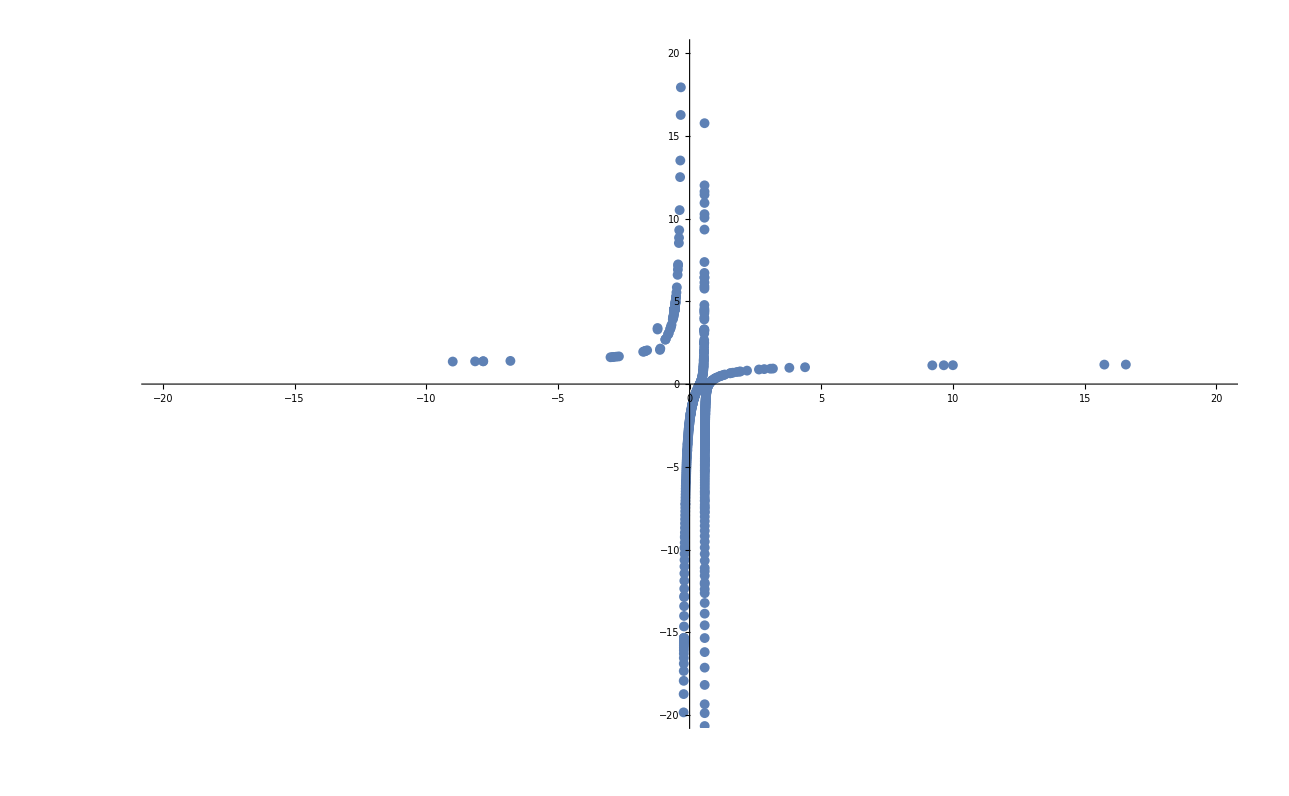

Scattered_02.csv

```mathematica
ListPlot[Re[Scattered], PlotRange->{{-20,20},{-20,20}}]
Export["Scattered_02.csv",Scattered]
```

```mathematica
Sections
```

{2.22235,4.43114,3.07945,2.66597,4.58287,3.57979,0.130184,3.21527,4.97407,4.00887,3.90366,5.84476,4.21478,4.77752,7.23072,4.30151,5.90247,9.29822,4.34836,7.37373,12.5044,4.37833,9.33401,17.9283,4.39927,12.0066,28.673,15.7607,58.652,4.42619,21.2548,496.019,4.43505,29.7882,-94.8912,44.3381,-47.7707,73.5693,-33.9244,157.898,-27.4299,2112.81,-23.7372,-235.696,-21.4056,-124.551,-19.8349,-90.3986,-18.73,-74.1388,-17.929,-64.8256,-17.3356,-58.9202,-16.8888,-54.9313,-16.5484,-52.1204,-16.2866,-50.0803,-16.0838,-48.5675,-15.926,-47.4279,-15.8025,-46.5591,-15.7056,-45.8907,-15.6294,-45.373,-15.5694,-44.9697,-15.522,-44.6544,-15.4845,-44.4069,-15.4548,-44.2122,-15.4314,-44.0588,-15.4127,-43.9376,-15.398,-43.8418,-15.3863,-43.766,-15.377,-43.706,-15.3696,-43.6584,-15.3638,-43.6207,-15.3591,-43.5908,-15.3555,-43.5671,-15.3525,-43.5483,-15.3502,-43.4033,-15.3323,-38.2859,-14.6442,-34.219,-14.0086,-30.9089,-13.4196,-28.1623,-12.8722,-25.8463,-12.3623,-23.867,-11.8859,-22.1557,-11.44,-20.6614,-11.0216,-19.3451,-10.6282,-18.1768,-10.2577,-17.1327,-9.90808,-16.1939,-9.5776,-15.3453,-9.26472,-14.5743,-8.96805,-13.8708,-8.68634,-13.2261,-8.41847,-12.6331,-8.16343,-12.0859,-7.9203,-11.5792,-7.68825,-11.1086,-7.46653,-10.6705,-7.25444,-10.2615,-7.05135,-9.87873,-6.85669,-9.51976,-6.66992,-9.18238,-6.49057,-8.86468,-6.31819,-8.56494,-6.15236,-8.28165,-5.99271,-8.01346,-5.83887,-7.75918,-5.69054,-7.5177,-5.5474,-7.28807,-5.40917,-7.06941,-5.27559,-6.86092,-5.14642,-6.66188,-5.02144,-6.47164,-4.90042,-6.2896,-4.78318,-6.11523,-4.66952,-5.94801,-4.55927,-5.7875,-4.45227,-5.63328,-4.34837,-5.48497,-4.24742,-5.3422,-4.14929,-5.20466,-4.05385,-5.07203,-3.96097,-4.94405,-3.87056,-4.82044,-3.78248,-4.70097,-3.69666,4.52422,-4.5854,-3.61298,4.52538,-4.47355,-3.53137,4.52653,-4.36519,-3.45173,4.52768,-4.26017,-3.37398,4.52883,-4.15829,-3.29804,4.52998,-4.05941,-3.22384,4.53114,-3.96338,-3.15131,4.53229,-3.87004,-3.08039,4.53344,-3.77928,-3.011,4.53459,-3.69097,-2.94309,4.53574,-3.60498,-2.8766,4.53689,-3.52121,-2.81147,4.53804,-3.43956,-2.74766,4.53919,-3.35992,-2.6851,4.54034,-3.2822,-2.62376,4.54149,-3.20632,-2.56358,4.54264,-3.13218,-2.50453,4.5438,-3.05972,-2.44655,4.54495,-2.98885,-2.3896,4.5461,-2.9195,-2.33365,4.54725,-2.8516,-2.27866,4.54841,-2.78509,-2.22459,4.54956,-2.7199,-2.17141,4.55072,-2.65597,-2.11908,4.55187,-2.59326,-2.06756,4.55303,-2.53169,-2.01683,4.55419,-2.47122,-1.96685,4.55535,-2.4118,-1.9176,4.55651,-2.35338,-1.86904,4.55767,-2.2959,-1.82114,4.55883,-2.23933,-1.77388,4.55999,-2.18362,-1.72723,4.56116,-2.12872,-1.68116,4.56233,-2.0746,-1.63565,4.56349,-2.02122,-1.59067,4.56466,-1.96852,-1.54619,4.56584,-1.91648,-1.50218,4.56701,-1.86506,-1.45864,-1.81421,-1.41551,-1.7639,-1.3728,-1.71409,-1.33046,-1.66475,-1.28847,-1.61584,-1.24682,-1.56733,-1.20546,-1.51916,-1.16439,-1.47132,-1.12356,-1.42375,-1.08297,-1.37643,-1.04257,-1.32931,-1.00234,-1.28235,-0.962255,-1.23551,-0.922283,-1.18874,-0.882391,-1.142,-0.842548,-1.09523,-0.802719,-1.04839,-0.762867,-1.00139,-0.722954,-0.954164,-0.682936,-0.90661,-0.642769,-0.858576,-0.602404,-0.809802,-0.561785,-0.75972,-0.520852,-0.706509,-0.479539,-0.637188,-0.43777,-0.678243,-0.39546,-0.586729,-0.352512,-0.529544,-0.308811,-0.475405,-0.264227,-0.421581,-0.218604,-0.367303,-0.171755,-0.312226,-0.123459,-0.256144,-0.0734428,-0.198904,-0.0213771,-0.140383,0.0331435,-0.0804781,0.0906128,-0.0190828,0.151628,0.0439167,0.216904,4.61779,0.1086,0.287278,4.61948,0.175721,0.363727,4.62123,0.244942,0.447393,4.62305,0.317212,0.53964,4.62496,0.393267,0.642163,4.62698,0.474134,0.757156,4.62914,0.561157,0.887566,4.63146,0.656103,1.03749,4.634,0.761336,1.2128,0.880112,1.4222,1.01709,1.67919,1.17923,2.00578,2.44047,1.37766,3.05723,1.63204,4.01856,1.98927,5.76467,2.06395,10.0498,3.05075,39.2784,5.19013,4.10443,-19.8819,8.84115,4.50333,-7.71063,91.5369,4.56831,-4.64748,-9.8649,4.59239,-3.22512,-4.39984,4.60536,-2.38538,-2.67546,4.61384,-1.8176,-1.81037,-1.39739,-1.27624,-1.06482,-0.90278,-0.784916,-0.617913,-0.565579,-0.385278,-0.344559,-0.183583,-0.149941,0.00183326,0.0281438,0.182736,0.192968,0.368643,0.348312,0.566351,0.499671,0.781434,0.652397,1.0208,0.81183,1.2947,0.983888,1.61897,1.17608,2.01932,2.54046,1.39929,3.26812,1.67184,4.39089,4.70229,2.03996,6.42261,4.72589,2.14563,11.44,4.78097,2.98646,47.9712,5.0313,3.90132,-21.7952,6.91699,16.2593,-32.9503,-2.77741,-4.00909,-2.13153,-2.56361,-1.6508,-1.75854,-1.26851,-1.23071,-0.947683,-0.846291,-0.641678,-0.543755,-0.427793,-0.289713,-0.195713,-0.0625151,0.017174,0.155232,0.213332,0.378413,0.396543,0.61732,0.573679,0.879619,0.751538,1.17513,0.936654,1.51911,1.13621,1.93614,2.46811,1.35951,3.19306,1.6209,4.27578,1.95111,6.13665,3.29808,10.2662,2.72281,28.625,4.89223,3.46787,-37.8855,5.53418,4.26404,-11.3121,8.52173,4.53049,-6.53544,24.5417,4.59721,-4.49395,-22.9965,-3.33385,-7.24634,-2.56626,-4.03045,-2.00591,-2.61338,-1.56672,-1.7946,-1.20282,-1.24578,-0.886288,-0.83989,-0.641777,-0.516567,-0.351962,-0.241862,-0.106882,0.00781739,4.69125,0.120389,0.253295,4.69546,0.331511,0.511959,4.69978,0.531154,0.795102,4.70431,0.727465,1.11354,4.70919,0.92783,1.48353,4.71462,1.13975,1.93148,4.72088,2.50254,1.37232,3.28099,1.63904,4.44533,1.96908,6.45308,3.38721,10.9422,2.68464,31.4946,4.89897,3.35363,-38.5867,5.30013,4.11986,-11.9979,7.15702,4.49652,-7.02886,13.508,4.59418,-4.88727,572.454,-3.66585,-12.8104,-2.85618,-5.91867,-2.26453,-3.61195,-1.80059,-2.4287,-1.41616,-1.68936,-1.08252,-1.16868,-0.778427,-0.769782,-0.515506,-0.442998,-0.24623,-0.157994,0.00691723,0.109373,0.244871,0.382655,0.468622,0.680133,0.685524,1.01518,0.90377,1.40513,1.1314,1.87813,2.48265,1.37768,3.30961,1.65591,4.55286,1.99605,6.71456,26.1573,11.6292,4.83971,2.69435,35.6395,4.92739,3.31977,-37.1309,5.24786,4.03238,-12.3945,6.6,4.46109,-7.42116,10.5101,4.5882,-5.24247,30.2081,4.63759,-3.99124,-29.3482,4.66376,-3.15907,-9.21506,4.68043}